# Developing a Dynamic Network-Based Model for COVID-19

## Christie Wilce, Ella Mattinen and Marcell Veiner

## Introduction & Background

• Significant uprise in epidemiological modelling, as a natural response to COVID-19.

• Such models are inherently imperfect and sensitive to the data they employ and the assumptions they are built on.

• Typical compartmental approach to epidemiological modelling: Susceptible-Infected-Recovered (SIR) model.
	• 	Explains the fundamental behaviour of a disease.
	• 	Fails to capture the response of society to it.
	
• Subdividing of compartments can be used to introduce basic demography to the modelled population, and parameters.

• We present a dynamic network-based model.

### Changing Circumstances

• Number of cases in the UK during the early days:
	• There is a steady rise in number of new cases per day as the disease enters the country.
	• Cases level off slightly after March 24th 2020.

• Many epidemic models would have predicted further spreading .

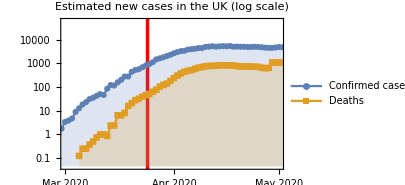

• Possible causes of inconsistency:
	• Introduction of the first lockdown in the UK.
	• Models are often fixed over time.

• Accounting for changes: 
	• Dataset of governmental measures and implementing these into the model.

## Building the Model

#### Small Worlds

• Goal: to model the spread of an epidemic through a population where connections between people are random
• Small-world property: if you choose two individuals anywhere on Earth, you will find a path of at most six acquaintances between them
	• In the language of network science this is described through the average path length, which has to grow proportionally to the number of nodes, and the clustering coefficient, which has to be closer to 1 (than 0).

• We obtain a small-world from Watts-Strogatz random graphs.
	•  If the probability of rewiring 𝓅 ≈ 0 : Watts-Strogatz model gives a regular ring lattice.
	• If 𝓅 ≈ 1 : model gives a random graph that is similar to a binomial random graph.
	• None of these cases posses the small-world property, and so choosing the correct 𝓅 in between these extremes is crucial.
	• We replicate the following result from [7] which helps us finding the right value for 𝓅.

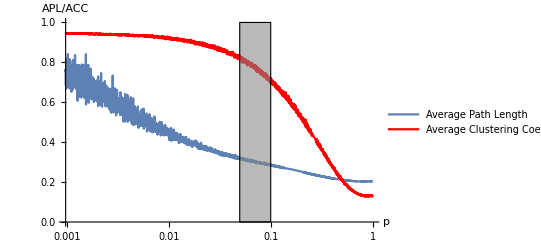

• We can conclude that a small value for 𝓅 is required for a small world graph.
	• A value between 0.05 and 0.1 is recommended.

```mathematica
p = 0.075;
```

#### Network Demography

• Benefit of discrete approaches like this one, is the ability to represent a non-homogenous population.
• We will introduce a simple demography to our model by assigning each node an age.
• We will assign the age of a person so that the age distribution in our network is similar to that in real life.

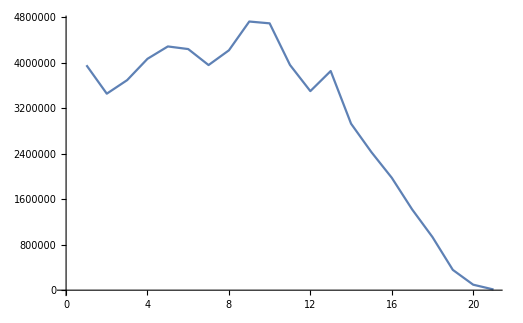

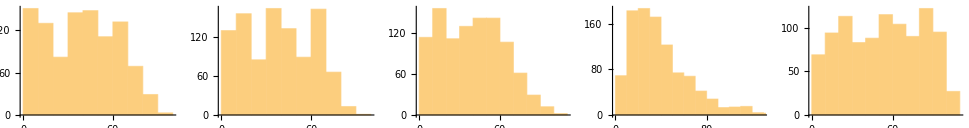

•  And so we have a distribution from which we can ask for a random variate and assign that as the age of a node.

Getting Infected

• We start by generating a small community.
• We obtain the friends or neighbours of a given person
• Distinguish between symptomatic and asymptomatic cases 
	•  Assume a random recovery time for each infected person
• Below the red nodes show symptoms but the yellow ones are asymptomatic

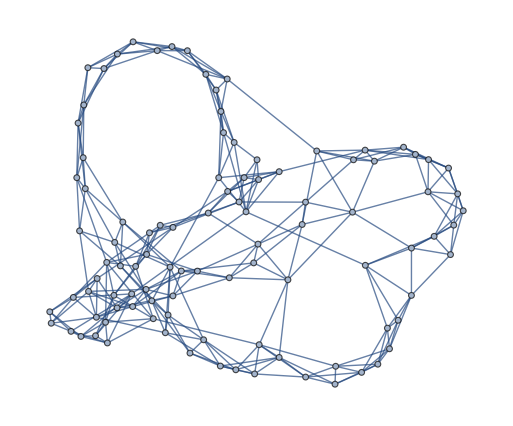
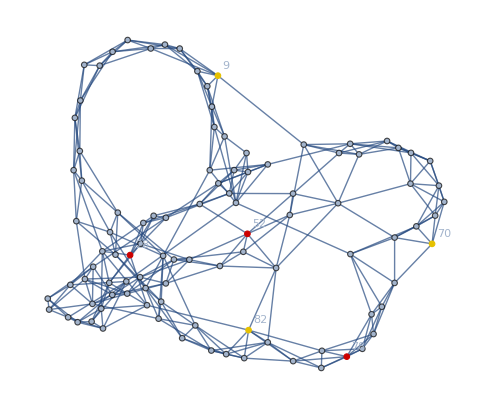
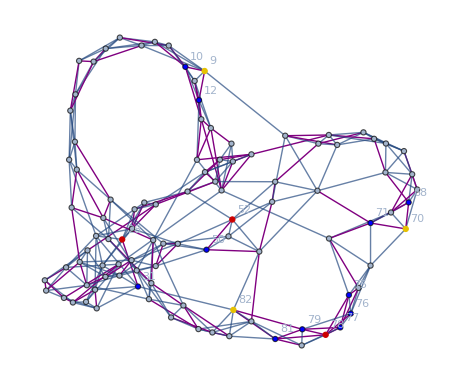

• Generate meetings between friends

• Above the blue nodes are meeting with infected and thus have a chance of becoming ill themselves
• Now, we will introduce a chance of infection:
	• Secondary attack rate = 60% 
	• Highly dependent on environment, thus assume close contact

• When incorporating this into our model we found 60% too high
• We will set the secondary attack rate to 40% as the model becomes more reliable and realistic

• We have also set 84% of the infected to show symptoms and the rest to be asymptomatic

Putting this all together compactly we get the following :

```mathematica
p = 0.075;infectionRate=0.4;symptomaticRate = 0.84;
pop=Dataset[WolframAlpha["age distribution in UK",{{"AgeDistributionPyramidGraphic:AgeDistributionData",1},"ComputableData"}]];
agePop=QuantityMagnitude[Normal[pop[[All,2]]]+ Normal[pop[[All,3]]]];
dists=FindDistribution[RandomChoice[agePop->Range[2,102,5],1000 ],5];
ageDist = dists[[4]];
gBasic=RandomGraph[WattsStrogatzGraphDistribution[100,p,3]];
avgRecovery = 10; 
agentNeighborhoods[g_]:=Merge[Catenate[
{#1->#2,#2->#1}&@@@EdgeList[g] (* Take every edge in g and create v -> u, u -> v *)
],                                                                   (* As we want v to be a neighbour of u and vica versa *)
Identity                                                                           (* Merge expects a merging function *)
]; 
recoveryTime =NormalDistribution[avgRecovery,3]; (* average recovery time around 10 days *) 
neighborsBasic=agentNeighborhoods[gBasic];
meetingCounts=AssociationThread[Keys[neighborsBasic],ExponentialDistribution[1]];
runStep[agentStates_,neighbors_,meetingCounts_,recoveryTime_]:= (* function to advance simulation by one step *)Module[{meetings,agentMeetings}, (* For local scoping: meetings and agentMeetings won't be accessible in other cells *)meetings=DeleteDuplicatesBy[Flatten[Function[a,{a,#}&/@RandomSample[neighbors[a],Clip[Round[RandomVariate[meetingCounts[a]]],{0,Length[neighbors[a]]}]]]/@Keys[neighbors],1],Sort];
agentMeetings=Merge[Catenate[{#1->#2,#2->#1}&@@@meetings],Identity];
AssociationMap[Replace[agentStates[#],{{n_,"S",m_}:>If[(MemberQ[Lookup[agentStates,agentMeetings[#]],{_,"Is",_}]||MemberQ[Lookup[agentStates,agentMeetings[#]],{_,"Ia",_}]) && RandomChoice[{infectionRate, 1-infectionRate}->{True, False}],
If[ RandomChoice[{symptomaticRate,1-symptomaticRate}->{True, False}],{n,"Is",Floor@RandomVariate[recoveryTime]},{n,"Ia",Floor@RandomVariate[recoveryTime]}],
{n,"S",m} ],
{n_,"Is",m_}:>If[m>0,{n,"Is",m-1},{n,"R",m}],
{n_,"Ia",m_}:>If[m>0,{n,"Ia",m-1},{n,"R",m}],
{n_,"R",m_}:>{n,"R",m} 
}]&,Keys[agentStates]]]
simulateBasic[neighbors_,meetingCounts_,recoveryTime_,initialInfected_,maxSteps_:Infinity]:=Module[{agentStates,steps},
agentStates=Join[
AssociationMap[{Floor@RandomVariate[ageDist],"S",-1}&,Keys[neighbors]],
AssociationMap[{Floor@RandomVariate[ageDist],"Is",Floor@RandomVariate[recoveryTime]}&,RandomSample[Keys[neighbors],initialInfected]],
AssociationMap[{Floor@RandomVariate[ageDist],"Ia",Floor@RandomVariate[recoveryTime]}&,RandomSample[Keys[neighbors],initialInfected]]
];
steps=NestWhileList[runStep[#,neighbors,meetingCounts,recoveryTime]&,agentStates,MemberQ[{_,"Is",_}] ,1,maxSteps];
{steps, meetings}]
sirPlot[sim_,opts___]:=StackedListPlot[Transpose[sim],Frame->{{True,False},{True,False}},FrameLabel->{"Days","Agents"},opts]
resBasic= simulateBasic[neighborsBasic, meetingCounts, recoveryTime, 5];
simulationBasic = resBasic[[1]]; meetings = resBasic[[2]];
Manipulate[HighlightGraph[gBasic,{Keys@Select[Part[simulationBasic,step],MatchQ[{_,"Is",_}]], Style[Keys@Select[Part[simulationBasic,step],MatchQ[{_,"R",_}]], Black],Style[Keys@Select[Part[simulationBasic,step],MatchQ[{_,"Ia",_}]], Yellow]}], {step, 1, Length[simulationBasic], 1}]
numbersBasic = {Count[#,{_,"Ia",_}]+Count[#,{_,"Is",_}],Count[#,{_,"S",_}],Count[#,{_,"R",_}]}&/@simulationBasic;
Manipulate[sirPlot[numbersBasic[[;;step]],PlotLegends->{"Infected (Combined)","Susceptible","Recovered"}],{step, 1, Length[numbersBasic], 1}]
```

Above is a typical SIR model over time

• It produces the typical curves for each compartment that one can see in the relevant literature
• Next we focus on expanding on this model

## Making the Model Dynamic

• Starting point is 01/02/2020 (Epidemic Data for Novel Coronavirus COVID-19 for UK has data starting from February).
• We create an association between dates and the corresponding measures put in place that day.

```mathematica
dates = measures[All, "ImplementationDate"] // DeleteMissing //Normal;
noDays ={31,29,31,30,31,30,31,31,30,31,30,31};
noDays=(#["Month"]-2)*Part[noDays,#["Month"]]+(#["Day"])&/@dates;
categories =Select[measures, Not[MissingQ[#ImplementationDate]]&][All, "Category"]//Normal;
measuresDays = Merge[DeleteDuplicates]@Thread@Rule[noDays,categories]
```

<|42→{Public health measures},44→{Social and economic measures},47→{Public health measures,Social distancing},49→{Public health measures},51→{Social and economic measures,Social distancing},52→{Social distancing},53→{Social distancing},55→{Lockdown,Movement restrictions,Social distancing}|>

• The duration of restrictions not in dataset. 
• We assume that each restriction is enforced for 30 days only. 
• We assume that each restriction in the same category affects the corresponding parameters by the same amount.

Now let us convince ourselves that the restrictions do work and they have an effect on the spread of the virus.

As we may observe the spread is directly affected by the restrictions, and although this model is still simple, it can sometimes produce the familiar second wave instead of a single peak, or simply a shorter one.

### Other Changes

### Reinfection

Although there is no consensus whether reinfection with the coronavirus is possible [4] we have added a small chance for recovered people to be susceptible again.

```mathematica
reinfectionRate =0.001;
```

### Death

The death rate of COVID varies across ages, we use the age distribution to distinguish the death rate between different age groups. The values for these were taken from [1] support of another study [6]. For example, the death rate for persons over the age of 80 was found to be 14.8% while for the younger population, age 10 to 39, it was found to be only 0.4%. But this is overall and not per day, so we should divide by the average number of infected days.

```mathematica
deathChance[m_] := Piecewise[{{0,9≥m},{0.002,39≥m≥10},{0.004,49≥m≥40},{0.013,59≥m≥50},{0.039,69≥m≥60},{0.08,79≥m≥70},{0.148,m≥80}}]/avgRecovery
```

### Vaccination

As vaccination is taken into consideration in our model, we must look at the rate at which the population gets vaccinated. Looking at the data provided by the UK Government [2], the average amount of daily 1st doses is around 300 000. If we take into account the 2nd doses, this average increases to 310 000, which accounts for 0.45% of the population. We will arbitrarily defined that vaccination starts after 60 days, this of course can be changed easily.

```mathematica
vaccinationRate=0.0045;vaccinationIntroduced = 60;
```

### Quarantine

Self-isolation (10 days) measures are taken in order to prevent the spread of the virus, however, studies show [3] that individuals may be infectious 1-3 days prior to showing any symptoms. This also supports the claim that secondary infections may occur through transmission between an asymptomatic and a susceptible individual. Studies also show that symptomatic individuals are most infectious during the first 7 days after symptoms begin [6]. Hence, in our model we assume that after each symptomatic person has been in a 10 day quarantine, they are no longer infectious.  We will also assume that there is a 10 day lenient period after introducing the measure, where people go to quarantine gradually.

```mathematica
quarantiningIntroduced =30;maxdaysFree=7;mindaysFree=3;
```

```mathematica
lenientPeriod=10;lenient[day_,quarantiningIntroduced_]:=Piecewise[{{1,day>quarantiningIntroduced+ lenientPeriod},{Rescale[day, {quarantiningIntroduced, quarantiningIntroduced+lenientPeriod}],quarantiningIntroduced+ lenientPeriod≥day≥quarantiningIntroduced},{0,quarantiningIntroduced> day}}]
```

### Communities

• Create a supergraph with random graph communities.
• We have adapted it so that it takes in the populations for each cluster, that is the number of nodes in the clusters.
• Use country data from wolfram to model a network of large cities in the UK.
• Scale city populations by scaling factor.

```mathematica
generateSupergraph[structure_,edgesSubgraph_,rewiring_,edgeThickness_,population_,scale_]:=
(* structure: supergraph, like a meshgraph 
  edgesSubgraph: the k parameter in Watts-Strogatz graph, i.e. number of neighbours / 2
  graphDistribution: the usualy random graph parameters
edgeThickness: number of edges connecting subgraphs
poulation: population for each community
scale: scaling factor for population
*)
Module[{clusters,g,previousCount=0,vertices,edges,connectingEdges, count=0,pop},
(* For compatibility, if population is only a number, create a list of it *)
pop=If[Length[population]>0, population, Table[population, VertexCount[structure]]];
clusters=Table[
Module[{cluster},
count +=1;(* for population indexing *)
cluster=IndexGraph[RandomGraph[WattsStrogatzGraphDistribution[Floor[pop[[count]]*scale], rewiring,edgesSubgraph]],previousCount];
previousCount+=VertexCount[cluster];
(* Above two lines create graph with vertices correctly indexed by numbers *)
(* Below line puts the vertices and edges of this graph in table *)
{VertexList[cluster],EdgeList[cluster]}],
(* For every node in the supergraph *)
{i,VertexCount[structure]}
];
(* 
	But clusters are {graph1, graph2, ...} 
   The line below converts this to {{all vertices}, {all edges}}
*)
{vertices,edges}=Union@@@Transpose[clusters];
(* Create random undirected edges connecting subclusters, first are the vertices hence composition *)
connectingEdges=UndirectedEdge@@RandomChoice@*First/@
clusters[[{#1,#2}]]& (* Gets the appropriate cluster *)
(* Creates edgeThicnkess number of copies of the mesh structure *)
@@@Catenate[ConstantArray[EdgeList[structure],edgeThickness]]; (* We will want to replace and add these edges to the graph *)
Graph[vertices,Join[edges,connectingEdges]]]
"Create Supergraph Defined"
```

Create Supergraph Defined

```mathematica
names=CityData[{Large,"UnitedKingdom"}];
citypop=QuantityMagnitude@ ( CityData[#,"Population"]& /@ names) ;
citycoords= CityData[#,"Coordinates"]& /@ names;
Needs["ComputationalGeometry`"]
dtri=DelaunayTriangulation[citycoords];
list={};Table[Do[AppendTo[list,{i, dtri[[All,2]][[i,j]]}],{j,1,Length[dtri[[All,2]][[i,All]]]}],{i,1,Length[dtri]}];
coupling=Table[0,{i,1,Length[names]},{j,1,Length[names]}];
For[i=1,i<Length[list]+1,i++, coupling[[list[[i]][[1]],list[[i]][[2]]]]=1;]
coupling=SparseArray[coupling];

ukSupergraph = generateSupergraph[IndexGraph@AdjacencyGraph[coupling],2,p,2,citypop,0.0001]
```

-Graphics-

### Performance and Last Changes

• Last changes before evaluation.
• Minor parallelisation changes.
• Removing graph data, only keep state counts. 
• Scale graphs down to sensible vertex counts.
• Try running code on Macleod.

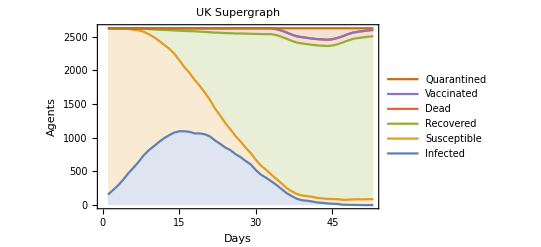

## Evaluation

• Compare how different parameters affect our UK Supergraph
	• Quarantining at earlier and later.
	• Changes in infection rates.
	• Changes in Symptomatic rates.
• Aim is to see the similarities and differences between our UK supergraph and real UK data.
•  Pinpointing the limitations of our model and how to improve in the future.

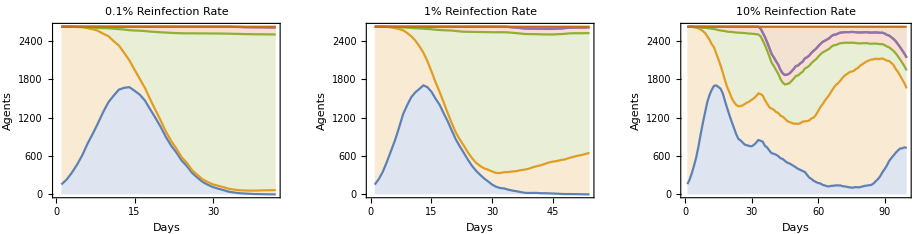

## Grid 30

• We can see there are limitations with our parameters as many graphs look and act the same.
• We can change the ‘quarantineIntroduced’ parameter to and earlier date.

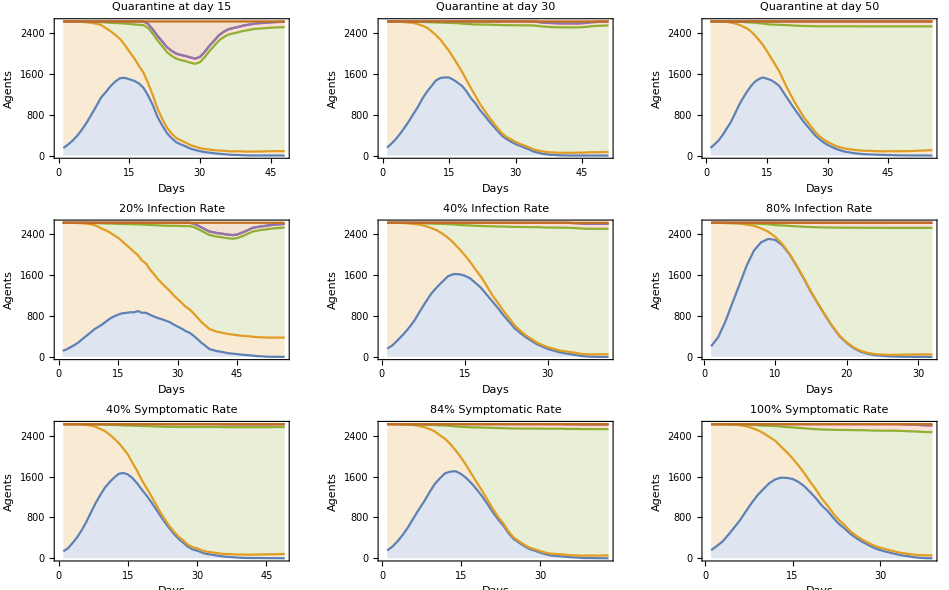

## Grid 15

• When quarantine is introduced earlier, there are less infected cases, and an increase in quarantined cases which results in a flattened curve of infection.
• Each time the infection rate doubles, the curve of infections steepens, resulting in a decrease in susceptible cases. The curve of the infection flattens due to infected cases falling into quarantine.
• As the symptomatic rate increases, the more cases there are of people in quarantine.

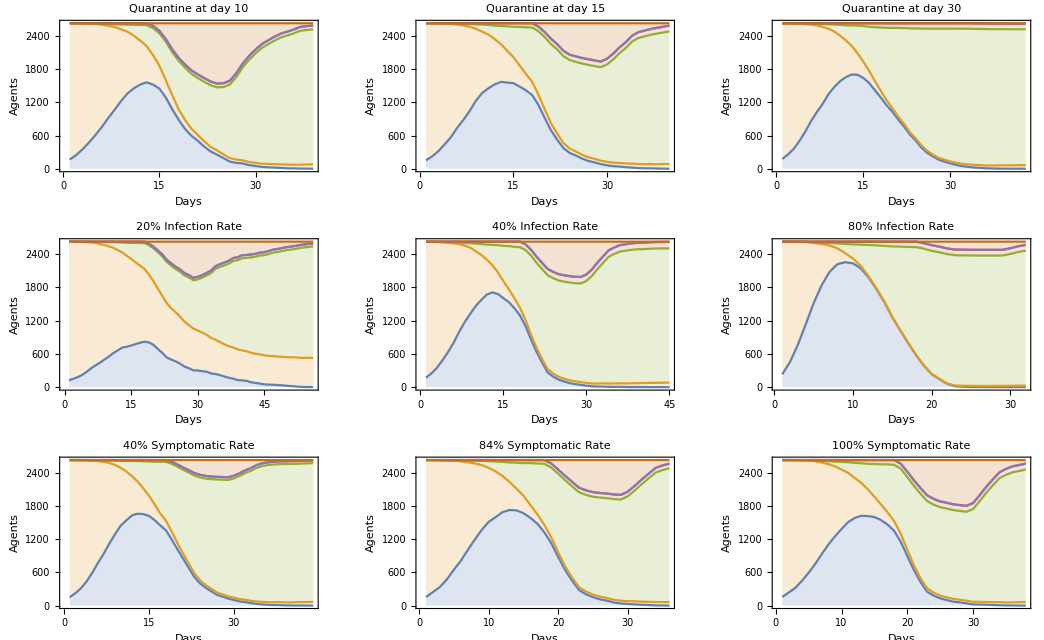

## Comparing UK Supergraph to Real Data

• Tuning the parameters to the true figures we have by our references: quarantine started on 24th March, therefore ‘quarantineIntroduced=52’; taking the lowest of the infection rates, we will refer to the ‘overnight camp’ study and set ‘infectionRate=0.44’; and our symptomatic rate is accurate so we shall keep that at ‘symptomaticRate=0.84’.
•  Transforming our SIR graph into a logarithmic we get:

• Our model follows the same trend as real data.
• Our model is not accurate - there is a decline in confirmed cases before quarantine introduced.
• Real data is also not fully accurate due to the anomalies during the first month.

## Conclusions & Future Work

Key limitations of our model which we wish to change with future work:

• Our model on Mathematica could not handle a large population size making the results less accurate.
• Do not have accurate data for the transmission rate of asymptomatic infection.
• We have not delved much into social networks or close contacts.

## References

[1]  Worldometer. Age, sex, existing conditions of covid-19 cases and deaths. https://www.worldometers.info/coronavirus/coronavirus-age-sex-demographics/.
[2]  GOV.UK. Uk coronavirus data. https://coronavirus.data.gov.uk/.
[3]  Stephen A Lauer, Kyra H Grantz, Qifang Bi, Forrest K Jones, Qulu Zheng,Hannah  R  Meredith,  Andrew  S  Azman,  Nicholas  G  Reich,  and  JustinLessler.  The incubation period of coronavirus disease 2019 (covid-19) frompublicly  reported  confirmed  cases:  estimation  and  application.Annals ofinternal medicine, 172(9):577–582, 2020.
[4]  Sayak Roy. Covid-19 reinfection: myth or truth?SN Comprehensive ClinicalMedicine, 2(6):710–713, 2020.
[5]  Kelvin   Kai-Wang   To,   Owen   Tak-Yin   Tsang,   Wai-Shing   Leung,   An-thony Raymond Tam, Tak-Chiu Wu, David Christopher Lung, Cyril Chik-Yan Yip, Jian-Piao Cai, Jacky Man-Chun Chan, Thomas Shiu-Hong Chik,et al.  Temporal profiles of viral load in posterior oropharyngeal saliva sam-ples and serum antibody responses during infection by sars-cov-2:  an obser-vational cohort study.The Lancet Infectious Diseases, 20(5):565–574, 2020.
[6]  Robert  Verity,  Lucy  C  Okell,  Ilaria  Dorigatti,  Peter  Winskill,  CharlesWhittaker,  Natsuko  Imai,  Gina  Cuomo-Dannenburg,  Hayley  Thompson,Patrick  GT  Walker,  Han  Fu,  et  al.   Estimates  of  the  severity  of  coron-avirus disease 2019:  a model-based analysis.The Lancet infectious diseases,20(6):669–677, 2020.
[7]  Duncan  J  Watts  and  Steven  H  Strogatz.   Collective  dynamics  of  ‘small-world’networks.nature, 393(6684):440–442, 1998.

# Thank you!

## Christie Wilce, Ella Mattinen and Marcell Veiner